```mathematica
SixTuple:={RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
```

```mathematica
dT[Tmat_,Sigma_]:=999
βT[Tmat_,Sigma_]:=999Degree
```

### Run common_funs.nb, then ES_FindSymGroups.nb

```mathematica
U6x6=unit/@Orthogonalize[{SixTuple,SixTuple,SixTuple,SixTuple,SixTuple,SixTuple}]; 
eigenvalues={RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]};
Tmat=U6x6.DiagonalMatrix[eigenvalues].Transpose[U6x6];
MatrixForm[ProjToVSigOfU[Tmat,id,ISO]]
PoissonOfTmatISO[%]
```

```mathematica
Eigenvalues[Tmat]
Eigenvalues[ProjToVSigOfU[Tmat,id,ISO]]
```

```mathematica
TextForSigmaSubspace[Sigma_,U_]:=SequenceForm[SubscriptBox[Style["𝒱",14,Bold],Sigma]//DisplayForm,"(",U,")"];
TextForScriptTsubSigma[Sigma_]:=SubscriptBox[Style["𝒯",Bold],Sigma]//DisplayForm;
```

### Define function to display output for T.

```mathematica
OutputForT[Tmat_]:=(
Print["β_MONO^T = ",Style[∠,19],"(T, ", TextForScriptTsubSigma[MONO],") = ",Round[βT[Tmat,MONO],.001]," = ",Round[βT[Tmat,MONO]/Degree,.01]^o];
Print["β_ISO^T  = ",Style[∠,19],"(T, ", TextForScriptTsubSigma[ISO],") = ",Round[βT[Tmat,ISO],.001]," = ",Round[βT[Tmat,ISO]/Degree,.01]^o];(* BETA *)
(*Print["T = ",MatrixForm[Round[Tmat,.001]]];*)
Print["T = ",MatrixForm[Tmat]];
Print["Eigenvalues of T: ",Eigenvalues[Tmat]];
(* Print["P",Style["(",18],"T, ",TextForSigmaSubspace[ISO,"I"],Style[")",18],
SequenceForm[" = ",MatrixForm[Round[ProjToVSigOfU[Tmat,id,ISO],.001]]]];*)
Print["Eigenvalues of closest ISO: ",Eigenvalues[ProjToVSigOfU[Tmat,id,ISO]]];
Print["Lame parameters for P",Style["(",18],"T, ",TextForSigmaSubspace[ISO,"I"],Style[")",18]," are λ = ",Round[λofTmatISO[ProjToVSigOfU[Tmat,id,ISO]],.001]" and μ = ",Round[μofTmatISO[ProjToVSigOfU[Tmat,id,ISO]],.001],
", Poisson is ",Round[PoissonOfTmatISO[ProjToVSigOfU[Tmat,id,ISO]],.001]];
)
```

### For a first attempt, take nMax = 5, say.

```mathematica
nMax=5;   (* 20 is too big for a first try *)
```

### Main loop over nMax elastic maps

```mathematica
βT[TmatOLD,MONO]=0;
Do[U6x6=unit/@Orthogonalize[{SixTuple,SixTuple,SixTuple,SixTuple,SixTuple,SixTuple}]; 
eigenvalues={RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]};
Tmat=U6x6.DiagonalMatrix[eigenvalues].Transpose[U6x6];  (* a stable elastic map *)
GetTempAndθ0σ0ϕ0[Tmat,MONO];
βT[Tmat,MONO]=Chop[ArcSin[(temp[Tmat,MONO][[1]])/NormMatrix[Tmat]],ChopT];
dT[Tmat,ISO]=Simplify[DistToVΣofU[Tmat,id,ISO]];
βT[Tmat,ISO]=Chop[Simplify[ArcSin[dT[Tmat,ISO]/NormMatrix[Tmat]]],ChopT];
TmatForHistogram[n]=Tmat;
BetaMONOforHistogram[n]=βT[Tmat,MONO]/Degree;
BetaISOforHistogram[n]=βT[Tmat,ISO]/Degree;
PoissonForHistogram[n]=PoissonOfTmatISO[ProjToVSigOfU[Tmat,id,ISO]];
If[Mod[n,100]==0,Print["n = ",n]];
If[βT[Tmat,MONO]>βT[TmatOLD,MONO],
nLast=n;
Print["n = ",n];
Print["β_MONO^T = ",Style[∠,19],"(T, ", TextForScriptTsubSigma[MONO],") = ",Round[βT[Tmat,MONO],.001]," = ",Round[βT[Tmat,MONO]/Degree,.01]^o];
Print["β_ISO^T  = ",Style[∠,19],"(T, ", TextForScriptTsubSigma[ISO],") = ",Round[βT[Tmat,ISO],.001]," = ",Round[βT[Tmat,ISO]/Degree,.01]^o];(* BETA *)
Print["T = ",MatrixForm[Round[Tmat,.001]]];
Print["P",Style["(",18],"T, ",TextForSigmaSubspace[ISO,"I"],Style[")",18],
SequenceForm[" = ",MatrixForm[Round[ProjToVSigOfU[Tmat,id,ISO],.001]]]];
Print["Lame parameters for P",Style["(",18],"T, ",TextForSigmaSubspace[ISO,"I"],Style[")",18]," are λ = ",Round[λofTmatISO[ProjToVSigOfU[Tmat,id,ISO]],.01]" and μ = ",Round[μofTmatISO[ProjToVSigOfU[Tmat,id,ISO]],.01],
", Poisson is ",Round[PoissonOfTmatISO[ProjToVSigOfU[Tmat,id,ISO]],.001]];
TmatOLD=Tmat; ] ,{n,nMax}];
Print["nLast = ",nLast];
```

### Histograms

```mathematica
nMax
Histogram[Table[BetaMONOforHistogram[n],{n,nMax}],AxesLabel->{Style["β_MONO",16],None},AxesOrigin->{0,0}]
Histogram[Table[BetaISOforHistogram[n],{n,nMax}],AxesLabel->{Style["β_ISO",16],None},AxesOrigin->{0,0}]
Histogram[Table[PoissonForHistogram[n],{n,nMax}],AxesLabel->{Style["ν",16],None}]
```

```mathematica
Graphics[Point/@Table[{BetaMONOforHistogram[n],PoissonForHistogram[n]},{n,nMax}],AspectRatio->1,Axes->True,AxesLabel->{Style["β_MONO",16],Style["ν",16]},AxesOrigin->{0,-1}]
Graphics[Point/@Table[{BetaISOforHistogram[n],PoissonForHistogram[n]},{n,nMax}],AspectRatio->1,Axes->True,AxesLabel->{Style["β_ISO",16],Style["ν",16]},AxesOrigin->{0,-1}]
l = Line[{{0,0},{15,35}}];
Graphics[{Point/@Table[{BetaMONOforHistogram[n],BetaISOforHistogram[n]},{n,nMax}],{Dashed,Red,l}},AspectRatio->1,Axes->True,AxesLabel->{Style["β_MONO",16],Style["β_ISO",16]},AxesOrigin->{0,0}]
```

### List some subsets

```mathematica
νmin=0.15;
βmin=10;
Print["νmin = ",νmin];
Print["βmin = ",βmin," (deg)"];
```

```mathematica
data=Table[{n,BetaMONOforHistogram[n],BetaISOforHistogram[n],PoissonForHistogram[n]},{n,nMax}];
```

### First few

```mathematica
TableForm[Join[{{"n"," β_MONO" ," β_ISO","Poisson ν"},{}},Take[data,5]]]
```

### Set with nu > numin

```mathematica
TableForm[Join[{{"n"," β_MONO" ," β_ISO","Poisson ν"},{}},Select[data,.15<#[[4]]&]]]
```

### Set with nu < -0.40

```mathematica
TableForm[Join[{{"n"," β_MONO" ," β_ISO","Poisson ν"},{}},Select[data,#[[4]]<-0.4&]]]
```

### Set with beta > betamin and nu > numin

```mathematica
TableForm[Join[{{"n"," β_MONO" ," β_ISO","Poisson ν"},{}},Select[data,And[νmin<#[[4]],βmin<#[[2]]]&]]]
```

```mathematica
Print["nLast = ",nLast];
MatrixForm[Round[TmatForHistogram[nLast],.001]]
Eigenvalues[%]
PoissonForHistogram[nLast]
```

### Analyze one particular Tmat. Here we pick the Tmat farthest from having any symmetry.

```mathematica
nPick=nLast;
(* nPick =1162; *)
```

```mathematica
Print["nPick = ",nPick];
Tmat=TmatForHistogram[nPick];
denominator=1;
Tmat==Transpose[Tmat]
MatrixForm[Round[Tmat,.001]]
```

#### Σ = MONO

```mathematica
OutputFor[Tmat,MONO]
```

#### Σ = ORTH

```mathematica
OutputFor[Tmat,ORTH]
```

#### Σ = TET

```mathematica
OutputFor[Tmat,TET]
```

#### Σ = CUBE

```mathematica
OutputFor[Tmat,CUBE]
```

#### Σ = TRIG

```mathematica
OutputFor[Tmat,TRIG]
```

#### Σ = XISO

```mathematica
OutputFor[Tmat,XISO]
```

#### Σ = ISO

```mathematica
OutputFor[Tmat,ISO]
```

```mathematica
denominator=1;
```

```mathematica
LatticeOfDTs[Tmat]
Print["[T] = ",1/denominator,MatrixForm[Round[denominator Tmat,.001]]];
```

```mathematica
Eigenvalues[Tmat]
```

#### This one was unstable . Good idea to keep this reminder.

ChopTol = 0.00001

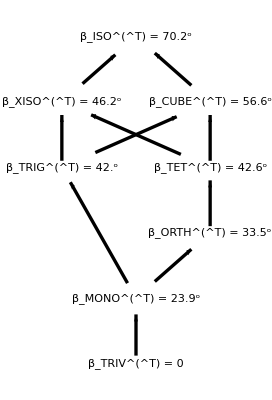

[T] = 1(-0.552 | 0.44 | -0.502 | -0.202 | 0.167 | 0.798
0.44 | 0.76 | -0.525 | 0.528 | -0.277 | -0.646
-0.502 | -0.525 | 0.7 | -0.306 | 0.693 | 0.918
-0.202 | 0.528 | -0.306 | -1.79 | -0.418 | 0.477
0.167 | -0.277 | 0.693 | -0.418 | 0.978 | 0.823
0.798 | -0.646 | 0.918 | 0.477 | 0.823 | -1.387)

```mathematica
Eigenvalues[({{-0.552, 0.44, -0.502, -0.202, 0.167, 0.798}, {0.44, 0.76, -0.525, 0.528, -0.277, -0.646}, {-0.502, -0.525, 0.7000000000000001, -0.306, 0.6930000000000001, 0.918}, {-0.202, 0.528, -0.306, -1.79, -0.418, 0.47700000000000004}, {0.167, -0.277, 0.6930000000000001, -0.418, 0.978, 0.8230000000000001}, {0.798, -0.646, 0.918, 0.47700000000000004, 0.8230000000000001, -1.387}})]
```

## List output for a set of Tmat

```mathematica
PrintOutputPair[Tmat_]:=(Print[Style["FOR T:",14]];
Print[OutputForT[Tmat]];
Print["   "];
Print[Style["FOR CLOSEST ISO TO T:",14]];
Print[OutputFor[Tmat,ISO]];
Print[Style["______________________________________________________________",Bold]];
Print["   "];)
```

#### Just to illustrate PrintOutputPair:

```mathematica
PrintOutputPair[TmatForHistogram[2]]
```

#### Set having both large beta and large nu

```mathematica
TβνSet[0,-1]:=Sort[Table[{TmatForHistogram[n],BetaMONOforHistogram[n],BetaISOforHistogram[n],PoissonForHistogram[n]},{n,nMax}],#1[[2]]>#2[[2]]&];
TβνSet[βmin_,νmin_]:=Select[TβνSet[0,-1],#[[2]]>βmin&& #[[4]]>νmin&];
```

#### Show what is in TβνSet :

```mathematica
Print["νmin = ",νmin];
Print["βmin = ",βmin," (deg)"];
Print[TableForm[Join[{{"                Tmat","  β_MONO","  β_ISO",Style["  ν",18]}},{" "},{MatrixForm[Round[#[[1]],.01]],#[[2]],#[[3]],#[[4]]}&/@TβνSet[βmin,νmin]]]];
```

#### Display a subset of the set

```mathematica
nSET = Length[TβνSet[βmin,νmin]]
```

```mathematica
nSHOW=nSET;
```

```mathematica
Print["nMax = ",nMax];
Print["νmin = ",νmin];
Print["βmin = ",βmin," (deg)"];
Print["Display ",nSHOW," T out of all ",nSET];
```

```mathematica
PrintOutputPair[#[[1]]]&/@Take[TβνSet[βmin,νmin],Min[nSHOW,Length[TβνSet[βmin,νmin]]]]
```